{{θ→InterpolatingFunction[{{0, 30.000000000000000000}}, <>],ϕ→InterpolatingFunction[{{0, 30.000000000000000000}}, <>]}}

Lagging Pendulum Coordinate Trajectories:

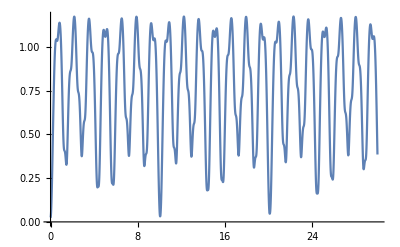

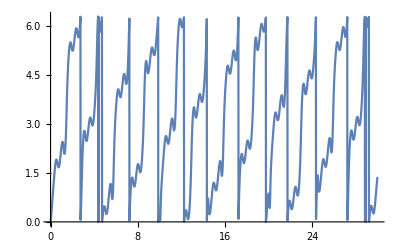

Lagging Pendulum Motion:

```mathematica
m=1/2;
l=3/2;
r=1/4;
ω=4Pi;
g=10;
x=r Cos[ω t]+l Sin[ϕ[t]]Cos[θ[t]];
y=r Sin[ω t]+l Sin[ϕ[t]]Sin[θ[t]];
z=-l Cos[ϕ[t]];
V=m g z;
vx=D[x,t];
vy=D[y,t];
vz=D[z,t];
T=(m/2)(vx^2+vy^2+vz^2);
ℒ=T-V;
time=30;

Needs["VariationalMethods`"]
eqs=EulerEquations[ℒ,{θ[t],ϕ[t]},t];
s=NDSolve[{eqs,θ[0]==Pi/128,ϕ[0]==Pi/128,θ'[0]==0,ϕ'[0]==0},{θ,ϕ},{t,0,time},WorkingPrecision->20]

"Lagging Pendulum Coordinate Trajectories:"
Plot[Evaluate[{ϕ[t]}/.s],{t,0,time}]
Plot[Mod[Evaluate[{θ[t]}/.s],2Pi],{t,0,time}]

"Lagging Pendulum Motion:"
plt=Plot3D[-10l,{x,-r-l,r+l},{y,-r-l,r+l},PlotRange->{-l-0.5,l}];
Animate[Show[plt,Graphics3D[{Red,Sphere[{(r) Cos[ω t]+l Sin[ϕ[t]]Cos[θ[t]],(r) Sin[ω t]+l Sin[ϕ[t]]Sin[θ[t]],-l Cos[ϕ[t]]},m/8]}],Graphics3D[{Line[{{r*Cos[ω*t],r*Sin[ω*t],0},{(r) Cos[ω t]+l Sin[ϕ[t]]Cos[θ[t]],(r) Sin[ω t]+l Sin[ϕ[t]]Sin[θ[t]],-l Cos[ϕ[t]]}}]}],Graphics3D[{Line[{{0,0,0},{r*Cos[ω*t],r*Sin[ω*t],0}}]}],BoxRatios->Automatic,Ticks->None]/.s,{t,0,time},AnimationRate->1, AnimationRunning->False,RefreshRate->120]
```

{{θ→InterpolatingFunction[{{0, 30.000000000000000000}}, <>],ϕ→InterpolatingFunction[{{0, 30.000000000000000000}}, <>],pθ→InterpolatingFunction[{{0, 30.000000000000000000}}, <>],pϕ→InterpolatingFunction[{{0, 30.000000000000000000}}, <>]}}

Lagging Pendulum Phase Space Trajectories:

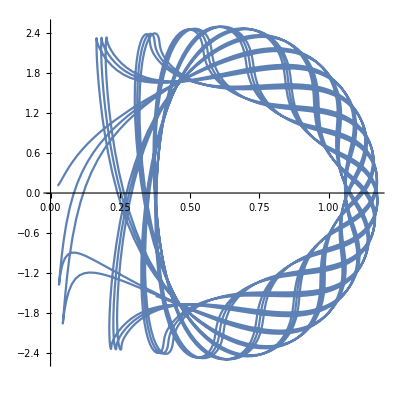

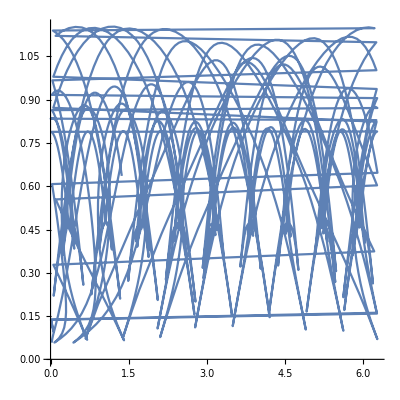

Lagging Pendulum Motion:

```mathematica
m=1/2;
l=3/2;
r=1/4;
ω=4Pi;
g=10;
ℋ=1/(2m l^2)(pϕ[t]^2+pθ[t]^2/Sin[ϕ[t]]^2)-(r ω)/l(pϕ[t]Cos[ϕ[t]]Sin[θ[t]-ω t]+(pθ[t]Cos[θ[t]-ω t])/Sin[ϕ[t]])+m/2 r^2 ω^2 Sin[θ[t]-ω t]^2(Cos[ϕ[t]]^2-1)-m g l Cos[ϕ[t]];
time=30;

eq1=ϕ'[t]==D[ℋ,pϕ[t]];
eq2=θ'[t]==D[ℋ,pθ[t]];
eq3=pϕ'[t]==-D[ℋ,ϕ[t]];
eq4=pθ'[t]==-D[ℋ,θ[t]];

s=NDSolve[{eq1,eq2,eq3,eq4,θ[0]==Pi/128,ϕ[0]==Pi/128,pθ[0]==m l r ω Sin[Pi/128]Cos[Pi/128],pϕ[0]==m l r ω Cos[Pi/64]Sin[Pi/64]},{θ,ϕ,pθ,pϕ},{t,0,time},WorkingPrecision->20]

"Lagging Pendulum Phase Space Trajectories:"
ParametricPlot[Evaluate[{ϕ[t],pϕ[t]}/.s],{t,0,time},AspectRatio->1]
ParametricPlot[Evaluate[{Mod[θ[t],2Pi],pθ[t]}/.s],{t,0,time},AspectRatio->1]

"Lagging Pendulum Motion:"
plt=Plot3D[-10l,{x,-r-l,r+l},{y,-r-l,r+l},PlotRange->{-l-0.5,l}];
Animate[Show[plt,Graphics3D[{Red,Sphere[{(r) Cos[ω t]+l Sin[ϕ[t]]Cos[θ[t]],(r) Sin[ω t]+l Sin[ϕ[t]]Sin[θ[t]],-l Cos[ϕ[t]]},m/8]}],Graphics3D[{Line[{{r*Cos[ω*t],r*Sin[ω*t],0},{(r) Cos[ω t]+l Sin[ϕ[t]]Cos[θ[t]],(r) Sin[ω t]+l Sin[ϕ[t]]Sin[θ[t]],-l Cos[ϕ[t]]}}]}],Graphics3D[{Line[{{0,0,0},{r*Cos[ω*t],r*Sin[ω*t],0}}]}],BoxRatios->Automatic,Ticks->None]/.s,{t,0,time},AnimationRate->1, AnimationRunning->False,RefreshRate->120]
```